```mathematica
NS["schizo_explore"]
```

```mathematica
(* definition of empirical covariance matrix, used a lot in the following *)covmatrix[data_]:=Block[{means=Mean@T@data,numindividuals=Length[data[[1]]]},
((data-means).T[data-means])/numindividuals]
```

```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\nanunana\\data_schizo170727"]
```

C:\Users\pglpm\repositories\nanunana\data_schizo170727

```mathematica
<<"reference_prior.m";
```

```mathematica
fileselect="5"; (* "reduced" *)
categories={"healthy","schizo"};
categoryfiles={"data_con"<>fileselect,"data_schizo"<>fileselect};
numcategories=Length[categories];
origquantities=Flatten@Import["data_params","CSV"];
orignumquantities=Length@origquantities;

Do[tempdata=Import[categoryfiles[[ii]],"CSV"];
(* transform 2nd moments to raw ones *)
Do[tempdata[[jj]]=Sqrt[tempdata[[jj]]+tempdata[[jj-6]]^2],{jj,7,12}];
(* transform 3nd moments to raw ones *)
Do[tempdata[[jj]]=CubeRoot[tempdata[[jj]]+3*tempdata[[jj-6]]^2*tempdata[[jj-12]]-2*tempdata[[jj-12]]^3],{jj,13,18}];
(* transform 4nd moments to raw ones *)
Do[tempdata[[jj]]=Surd[tempdata[[jj]]+4*tempdata[[jj-6]]^3*tempdata[[jj-18]]-6*tempdata[[jj-12]]^2*tempdata[[jj-18]]^2+3*tempdata[[jj-18]]^4,4],{jj,19,24}];

origsubjectfile[ii]=N@tempdata;
numindividuals[ii]=Length[origsubjectfile[ii][[1]]],
{ii,numcategories}];
(* one row for each quantity, one column for each individual *)
minnumindividuals=Min@Table[numindividuals[ii],{ii,numcategories}];
```

```mathematica
Do[If[aa<bb,plot=ListPlot[Table[T@origsubjectfile[ii][[{aa,bb},;;]],{ii,numcategories}],PlotRange->All(*{{0,All},{0,All}}*),PlotMarkers->{{Style["*",Bold],10},{Style["o",Bold],10}},Frame->True,FrameTicks->True,FrameLabel->origquantities[[{aa,bb}]]];
expng["visualize_data5\\expldata-"<>ToString[aa]<>"_"<>ToString[bb],plot];,Null];
,{aa,{1,4,10,16,22}},{bb,24}]
```

```mathematica
(* renormalize data for numerical stability *)

(* collect all data from all categories first *)
totaldata={};Do[totaldata=Join[totaldata,T[origsubjectfile[ii]]],{ii,numcategories}];
 (* individuals are in one column *)

tempmeans=Mean@totaldata;
totaldata=T@totaldata/tempmeans;

(* now renormalize and standardize *)
Do[origsubjectfile[ii]=origsubjectfile[ii]/tempmeans,{ii,numcategories}]

(* renormalize and standardize reference prior parameters *)
(*referencemeans=referencemeans/tempmeans;*)
(*referencecovariance=DiagonalMatrix[1/tempstds].referencecovariance.DiagonalMatrix[1/tempstds];*)
```

```mathematica
Do[data6[ii]=Apply[Times,origsubjectfile[ii]],{ii,numcategories}];
```

```mathematica
data6[1]
```

{244626.,7168.34,9.68854×10^6,711859.,4.73341×10^7,5.82341×10^7,8.94495×10^6,54685.7,1.24251×10^8,1.06785×10^8,1.7335×10^8,1.87828×10^6,6.7696×10^7,833195.,2.95036×10^8,9.93747×10^6,9.73563×10^7,9.92125×10^7,1.97566×10^6,41956.1,5.59753×10^7,2.19786×10^7,448411.,130368.,5.02969×10^6,2.41739×10^6,6.04454×10^7,2.15144×10^6,636.674,4.59457×10^8,293130.,6.49423×10^7,9.91553×10^6,7.91221×10^7,1.70163×10^8,2.4978×10^6,1.25975×10^7,1.67117×10^6,597077.,7.17694×10^6,3.61096×10^7,960153.,4.48767×10^6,1.95236×10^7,1.64894×10^7,2.17698×10^7,1.25463×10^8,7.27029×10^6,183703.,1.86465×10^6,72282.7,1.87009×10^8,2.14974×10^6,3.26406×10^7,1.16934×10^6,8.49728×10^7}

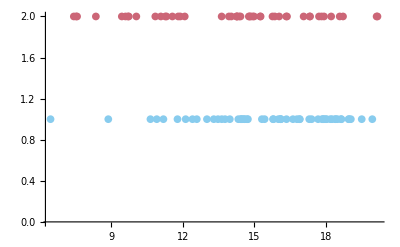

```mathematica
ListPlot[{T@{Log@data6[1],Table[1,numindividuals[1]]},T@{Log@data6[2],Table[2,numindividuals[2]]}}]
```

```mathematica
origsubjectfile[1][[{1,2},;;]]//MF
```

(0.758029 | 0.675088 | 0.852063 | 0.784907 | 0.894786 | 0.903643 | 0.850916 | 0.719425 | 0.917907 | 0.919075 | 0.928697 | 0.808815 | 0.902458 | 0.793282 | 0.944692 | 0.852909 | 0.910941 | 0.9132 | 0.81253 | 0.718038 | 0.896684 | 0.872877 | 0.775716 | 0.743499 | 0.831074 | 0.810508 | 0.899627 | 0.80872 | 0.610898 | 0.95524 | 0.77252 | 0.903004 | 0.848974 | 0.906702 | 0.929063 | 0.820205 | 0.857517 | 0.80165 | 0.779202 | 0.838595 | 0.886659 | 0.799495 | 0.829226 | 0.870926 | 0.864641 | 0.874784 | 0.916878 | 0.843664 | 0.753461 | 0.806436 | 0.730412 | 0.929843 | 0.813457 | 0.882339 | 0.80294 | 0.910465
1.20385 | 1.34973 | 1.04667 | 1.14498 | 0.996083 | 0.987291 | 1.04945 | 1.25684 | 0.969021 | 0.968529 | 0.958027 | 1.10646 | 0.986808 | 1.12969 | 0.941749 | 1.04593 | 0.976813 | 0.974626 | 1.10104 | 1.25342 | 0.992691 | 1.02036 | 1.15724 | 1.2078 | 1.0749 | 1.10333 | 0.99296 | 1.10339 | 1.51264 | 0.930879 | 1.17434 | 0.986587 | 1.05064 | 0.981259 | 0.957721 | 1.09134 | 1.04035 | 1.11743 | 1.14994 | 1.06239 | 1.00459 | 1.12517 | 1.07832 | 1.02366 | 1.03073 | 1.02195 | 0.970134 | 1.05997 | 1.19871 | 1.10993 | 1.24147 | 0.956663 | 1.10186 | 1.00933 | 1.12199 | 0.978566)

```mathematica
plot=ListPlot[Table[T@origsubjectfile[ii][[{1,2},;;]],{ii,numcategories}],PlotRange->Auto(*{{0,All},{0,All}}*),PlotMarkers->{{○,20},{△,20}}];
expng["expldata-1_2",plot];
```

```mathematica
gamma[s_,a_,b_]=Assuming[s>0,FS@PDF[GammaDistribution[a,b],s]]
```

(b^-a ⅇ^(-s/b) s^(-1+a))/Gamma[a]

```mathematica
gamma[s_,a_,b_]=Assuming[0<s<1,FS@PDF[BetaDistribution[a,b],s]]
```

((1-s)^(-1+b) s^(-1+a))/Beta[a,b]

```mathematica
ClearAll[test];Do[test[ii]=Assuming[a>0&&b>0,FS@Total@Log[gamma[origsubjectfile[ii][[1]],a,b]]];,{ii,numcategories}]
```

```mathematica
Array[test,2]
```

{118.423-9.98142 a-108.442 b+56 Log[1/Beta[a,b]],93.4562-10.9605 a-82.4957 b+48 Log[1/Beta[a,b]]}

```mathematica
co[1]=NIntegrate[Exp[test[1]],{a,0,+Infinity},{b,0,+Infinity},AccuracyGoal->Infinity,PrecisionGoal->10]
```

1.2385×10^32

```mathematica
co[2]=NIntegrate[Exp[test[2]],{a,0,+Infinity},{b,0,+Infinity},AccuracyGoal->Infinity,PrecisionGoal->10]
```

1.15541×10^23

```mathematica
Plot3D[Evaluate@{Exp[test[1]]/co[1],Exp[test[2]]/co[2]},{a,0,50},{b,0,10},AxesLabel->Auto,PlotPoints->70,PlotStyle->{{blue,Opacity[0.75]},{red,Opacity[0.75]}},PlotRange->{0,All},ViewPoint->Dynamic[viewpoint],Mesh->None]
```

-Graphics3D-

```mathematica
expng["estbeta",%194];
```

```mathematica
coj[1]=NIntegrate[Exp[test[1]]/((a+b)*(1+a+b)),{a,0,+Infinity},{b,0,+Infinity},AccuracyGoal->Infinity,PrecisionGoal->2]
```

1.74039×10^29

```mathematica
coj[2]=NIntegrate[Exp[test[2]]/((a+b)*(1+a+b)),{a,0,+Infinity},{b,0,+Infinity},AccuracyGoal->Infinity,PrecisionGoal->2]
```

1.1456×10^20

```mathematica
Plot3D[Evaluate@{Exp[test[1]]/((a+b)*(1+a+b))/coj[1],Exp[test[2]]/((a+b)*(1+a+b))/coj[2]},{a,0,50},{b,0,10},AxesLabel->Auto,PlotPoints->70,PlotStyle->Opacity[0.5],PlotRange->{0,2*10^-1},ViewPoint->Dynamic[viewpoint],Mesh->None]
```

```mathematica
Plot3D[Evaluate@{test[1],test[1]-Log[(a+b)*(1+a+b)]},{a,0,100},{b,0,100},AxesLabel->Auto,PlotPoints->70,PlotStyle->Opacity[0.5],PlotRange->{-50,All},ViewPoint->Dynamic[viewpoint]]
```

```mathematica
test1=Assuming[a>0&&b>0,FS@Total@Log[gamma[origsubjectfile[1][[1]],a,b]]]
```

118.423-9.98142 a-108.442 b+56 Log[1/Beta[a,b]]

```mathematica
max1=NMaximize[{test1,a>0&&b>0},{a,b}]
```

{46.8821,{a→104.595,b→0.0102757}}

```mathematica
test2=Assuming[a>0&&b>0,FS@Total@Log[gamma[origsubjectfile[2][[2]],a,b]]]
```

Log[(0.00270307 369.95^a b^(-48 a) ⅇ^(-54.6605/b))/Gamma[a]^48]

```mathematica
max2=NMaximize[{test2,a>0&&b>0},{a,b}]
```

{29.2594,{a→74.2839,b→0.0153299}}

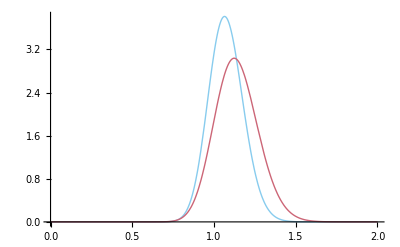

```mathematica
Plot[{gamma[s,a,b]/.max1[[2]],gamma[s,a,b]/.max2[[2]]},{s,0,2},PlotRange->All]
```

```mathematica
pr[1,s_]:=NIntegrate[gamma[s,a,b]*Exp[test[1]-Log[co[1]]],{a,0,+Infinity},{b,0,+Infinity},AccuracyGoal->Infinity,PrecisionGoal->5]
```

```mathematica
pr[2,s_]:=NIntegrate[gamma[s,a,b]*Exp[test[2]-Log[co[2]]],{a,0,+Infinity},{b,0,+Infinity},AccuracyGoal->Infinity,PrecisionGoal->8]
```

```mathematica
Plot[{pr[1,s],pr[2,s]},{s,0,1},PlotRange->All,PlotPoints->5]
```

$Aborted

```mathematica
expng["postdistr-1"]
```

```mathematica
ClearAll[test,max];Do[Do[test=Assuming[a>0&&b>0,FS@Total@Log[gamma[origsubjectfile[jj][[ii]],a,b]]];
max[jj]=NMaximize[{test,a>0&&b>0},{a,b}];,{jj,numcategories}];

plot=Plot[Evaluate@Table[gamma[s,a,b]/.max[jj][[2]],{jj,numcategories}],{s,0,1},PlotRange->All,PlotLabel->mylabels[{origquantities[[ii]]}]];
expng["mldistr-"<>ToString[ii],plot];,{ii,{1,3,5,11,17,23}}]
```

```mathematica
test1/.{a->150,b->0.0055}
```

-1669.04

```mathematica
(* improper prior *)
{referencenumber ,referencemeans,referencecovariance}= {0,Table[0,{orignumquantities}],Table[0,{orignumquantities},{orignumquantities}]};
```

```mathematica
fileh=origsubjectfile[1];filea=origsubjectfile[2];
```

```mathematica
minnumindividuals
```

48

```mathematica
orignumquantities
```

24

```mathematica
(* renormalize data for numerical stability *)

(* collect all data from all categories first *)
totaldata={};Do[totaldata=Join[totaldata,T[origsubjectfile[ii]]],{ii,numcategories}];
 (* individuals are in one column *)

tempmeans=Mean@totaldata;
totaldata=T@totaldata/tempmeans;

(* now renormalize and standardize *)
Do[origsubjectfile[ii]=origsubjectfile[ii]/tempmeans,{ii,numcategories}]

(* renormalize and standardize reference prior parameters *)
referencemeans=referencemeans/tempmeans;
(*referencecovariance=DiagonalMatrix[1/tempstds].referencecovariance.DiagonalMatrix[1/tempstds];*)
```

```mathematica
fileh=origsubjectfile[1];filea=origsubjectfile[3];
```

```mathematica
(* Pareto II distribution, obtained as gamma mixture of exponentials*)par[x_,a_,b_]=PDF[ParetoDistribution[b,a,0],x];
```

```mathematica
(* means and number of samples, for pareto distr *)Do[omeans[ii]=Mean@T[origsubjectfile[ii]];onind[ii]=numindividuals[ii],{ii,numcategories}];
```

```mathematica
(* product of Paretos for the quantities *)ClearAll[prob];
prob[x_,cat_]:=Product[par[x[[ii]],onind[cat],onind[cat]*omeans[cat][[ii]]],{ii,orignumquantities}];
```

```mathematica
Do[
success[cati]=Table[
(*success=0;
avdistr=Table[0,{ii,numcategories}];*)
datum=T[origsubjectfile[cati]][[ii]];
(*Print[datum];
Print[prob[datum,1]];
Print[par[datum[[1]],onind[1],onind[1]*omeans[1][[1]]]];
Print[par[datum[[1]],onind[2],onind[2]*omeans[2][[1]]]];*)
distr=Normalize[Table[prob[datum,jj],{jj,numcategories}],Total]

(*If[Last@Ordering[distr,-1]==cati,++success,Null];
avdistr=avdistr+distr;*)
,{ii,numindividuals[cati]}];
,{cati,2}]
```

```mathematica
success[1]//MF
```

(0.359168 | 0.640832
0.207514 | 0.792486
0.585994 | 0.414006
0.436239 | 0.563761
0.672638 | 0.327362
0.687288 | 0.312712
0.581026 | 0.418974
0.298661 | 0.701339
0.72003 | 0.27997
0.718822 | 0.281178
0.738953 | 0.261047
0.492138 | 0.507862
0.689253 | 0.310747
0.454646 | 0.545354
0.766485 | 0.233515
0.58625 | 0.41375
0.706895 | 0.293105
0.710105 | 0.289895
0.498625 | 0.501375
0.30295 | 0.69705
0.678799 | 0.321201
0.62986 | 0.37014
0.41794 | 0.58206
0.353934 | 0.646066
0.542491 | 0.457509
0.498736 | 0.501264
0.681761 | 0.318239
0.497147 | 0.502853
0.0807556 | 0.919244
0.785185 | 0.214815
0.393291 | 0.606709
0.689022 | 0.310978
0.58124 | 0.41876
0.698014 | 0.301986
0.739114 | 0.260886
0.513411 | 0.486589
0.59711 | 0.40289
0.478592 | 0.521408
0.428477 | 0.571523
0.56207 | 0.43793
0.657179 | 0.342821
0.461711 | 0.538289
0.536502 | 0.463498
0.624175 | 0.375825
0.61274 | 0.38726
0.630131 | 0.369869
0.718775 | 0.281225
0.564819 | 0.435181
0.364238 | 0.635762
0.488236 | 0.511764
0.314266 | 0.685734
0.741438 | 0.258562
0.499333 | 0.500667
0.649468 | 0.350532
0.46896 | 0.53104
0.703152 | 0.296848)

```mathematica
success[2]//MF
```

(0.487098 | 0.512902
0.796201 | 0.203799
0.307786 | 0.692214
0.520412 | 0.479588
0.308004 | 0.691996
0.193296 | 0.806704
0.44818 | 0.55182
0.599311 | 0.400689
0.596046 | 0.403954
0.251474 | 0.748526
0.528335 | 0.471665
0.470695 | 0.529305
0.524226 | 0.475774
0.64986 | 0.35014
0.534673 | 0.465327
0.128635 | 0.871365
0.463731 | 0.536269
0.169864 | 0.830136
0.484905 | 0.515095
0.699169 | 0.300831
0.479881 | 0.520119
0.725322 | 0.274678
0.453497 | 0.546503
0.30029 | 0.69971
0.638617 | 0.361383
0.359968 | 0.640032
0.5644 | 0.4356
0.237093 | 0.762907
0.274857 | 0.725143
0.792037 | 0.207963
0.652214 | 0.347786
0.312578 | 0.687422
0.515835 | 0.484165
0.225526 | 0.774474
0.505115 | 0.494885
0.135236 | 0.864764
0.512818 | 0.487182
0.338841 | 0.661159
0.480119 | 0.519881
0.310366 | 0.689634
0.684023 | 0.315977
0.670276 | 0.329724
0.679709 | 0.320291
0.235531 | 0.764469
0.583726 | 0.416274
0.71724 | 0.28276
0.565494 | 0.434506
0.348523 | 0.651477)

```mathematica
Mean@success[1]
```

{0.555281,0.444719}

```mathematica
Mean@success[2]
```

{0.467938,0.532062}

```mathematica
FS@Solve[{u==a/(a+b),v==a*b/((a+b)^2*(a+b+1))},{a,b}]
```

{{a→-(u ((-1+u) u+v))/v,b→-1+u+((-1+u)^2 u)/v}}

```mathematica
al[u_,v_]=u/v*(u*(1-u)-v)
```

(u ((1-u) u-v))/v

```mathematica
be[u_,v_]=(1-u)/v*(u*(1-u)-v)
```

((1-u) ((1-u) u-v))/v

```mathematica
detau=FS@Det@{{D[al[u,v],u],D[al[u,v],v]},{D[be[u,v],u],D[be[u,v],v]}}
```

-((-1+u) u ((-1+u) u+v))/v^3

```mathematica
FS[(1/(detau*v))/.{u->a/(a+b),v->a*b/((a+b)^2*(a+b+1))}]
```

-1/((a+b) (1+a+b))